```mathematica
ClearAll["Global``*"]
```

Inseriamo i dati del nostro sistema TC:

```mathematica
A={{-120, 70, -103, 36}, {-120, 70, -104, 35}, {0, -1, 1, 1}, {-120, 71, -105, 
35}}
B={{1}, {1}, {0}, {1}}
C1={{1, 0, -1, -1}}
```

{{-120,70,-103,36},{-120,70,-104,35},{0,-1,1,1},{-120,71,-105,35}}

{{1},{1},{0},{1}}

{{1,0,-1,-1}}

## 1.Calcolo dei modi naturali

```mathematica
λ= Eigenvalues[A]
```

{-5,-4,-3,-2}

```mathematica
pA = Factor[CharacteristicPolynomial[A,λc]]
```

(2+λc) (3+λc) (4+λc) (5+λc)

```mathematica
Solve[pA ==0]
```

{{λc→-5},{λc→-4},{λc→-3},{λc→-2}}

gli autovalori, calcolati prima con la funzione built-in e poi per definizione sono tutti reali e distiniti dunque i modi natuali corrispondenti sono del tipo e^(λt):

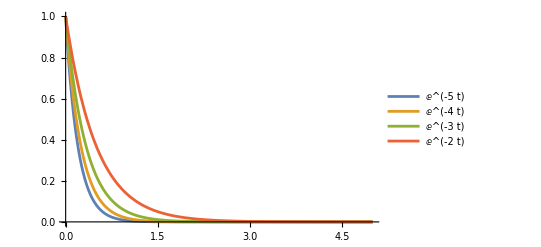

```mathematica
Plot[{ⅇ^(-5t),ⅇ^(-4t),ⅇ^(-3t),ⅇ^(-2t)},{t,0,5},PlotRange->All,PlotLegends->"Expressions"]
```

## 2.Analizziamo la risposta libera

```mathematica
x0 = {{2},{-3},{0},{-1}}
```

{{2},{-3},{0},{-1}}

```mathematica
MatrixForm[x0]
```

(2
-3
0
-1)

supponiamo che x0 sia lo stato iniziale per definizione di risposta libera avremo: x_l(t) = e^(At)x0 la risposta libera nello stato,  y(t) = C x_l(t) la risposta libera nell’uscita

```mathematica
T = Transpose[Eigenvectors[A]]
```

{{129,67,29,9},{155,84,39,14},{5,4,3,2},{125,64,27,8}}

```mathematica
z0 = Inverse[T].x0
```

{{89/6},{-109/2},{141/2},{-203/6}}

```mathematica
{n,n}=Dimensions[A]
```

{4,4}

```mathematica
Subscript[x, l][t_]:=FullSimplify[∑_(i=1)^n T[[All,i]] ⅇ^(λ[[i]]t)z0[[i,1]]]
```

```mathematica
MatrixForm[Subscript[x, l][t]]
```

(1/2 ⅇ^(-5 t) (3827-ⅇ^t (7303+87 ⅇ^t (-47+7 ⅇ^t)))
1/6 ⅇ^(-5 t) (13795-ⅇ^t (27468+ⅇ^t (-16497+2842 ⅇ^t)))
-1/6 ⅇ^(-5 t) (-1+ⅇ^t) (445+ⅇ^t (-863+406 ⅇ^t))
1/6 ⅇ^(-5 t) (11125-ⅇ^t (20928+ⅇ^t (-11421+1624 ⅇ^t))))

applicando un expand:

```mathematica
MatrixForm[Expand[Subscript[x, l][t]]]
```

((3827 ⅇ^(-5 t))/2-(7303 ⅇ^(-4 t))/2+(4089 ⅇ^(-3 t))/2-(609 ⅇ^(-2 t))/2
(13795 ⅇ^(-5 t))/6-4578 ⅇ^(-4 t)+(5499 ⅇ^(-3 t))/2-(1421 ⅇ^(-2 t))/3
(445 ⅇ^(-5 t))/6-218 ⅇ^(-4 t)+(423 ⅇ^(-3 t))/2-(203 ⅇ^(-2 t))/3
(11125 ⅇ^(-5 t))/6-3488 ⅇ^(-4 t)+(3807 ⅇ^(-3 t))/2-(812 ⅇ^(-2 t))/3)

notiamo che in ogni riga sono presenti tutti i modi naturali del sistema, ciò è dato dal fatto che lo stato iniziale x0 è 
dipendente da tutte le colonne della matrice di cambiamento di base T

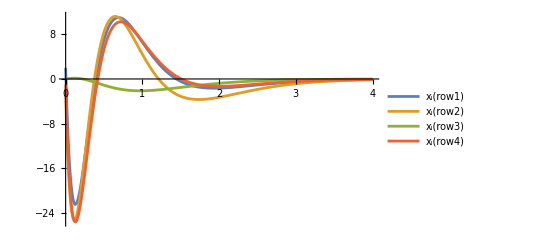

```mathematica
Plot[Evaluate[Subscript[x, l][t]],{t,0,4},PlotRange->All, PlotLegends->{"x_l(row1)","x_l(row2)","x_l(row3)","x_l(row4)"}]
```

valutiamo ora la risposta libera nell’uscita del sistema : y(t) = C x_l(t)

```mathematica
Subscript[y, l][t_]:= Simplify[C1.Subscript[x, l][t]]
```

```mathematica
C1.T
```

{{-1,-1,-1,-1}}

```mathematica
Subscript[y, l][t]
```

{1/6 ⅇ^(-5 t) (-89+327 ⅇ^t-423 ⅇ^(2 t)+203 ⅇ^(3 t))}

```mathematica
Expand[Subscript[y, l][t]]
```

{-89/6 ⅇ^(-5 t)+(109 ⅇ^(-4 t))/2-(141 ⅇ^(-3 t))/2+(203 ⅇ^(-2 t))/6}

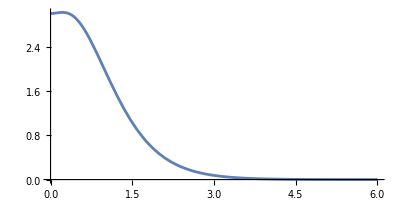

```mathematica
Plot[Subscript[y, l][t],{t,0,6},PlotRange->All,AspectRatio->Automatic]
```

## 3. Studiare la configurazione degli stati iniziali che attivano sulla risposta libera alcuni modi naturali ed altri no

Come detto in precedenza la presenza o meno di determinati modi naturali varia in base : dipendenza lineare tra lo stato iniziale x0 e le colonne di T. Sappiamo inoltre che le colonne di T sono autovettori di A e ad ogni autovettore corrisponde un autovalore. Detto ciò andiamo a scegliere delle configurazioni di stato iniziali linearmente dipendenti dalla prima(legata al primo modo naturale) e poi dalle altre. L’unico vettore linearmente indipendente che messo come stato iniziale “azzera” la risposta libera è il vettore banale poiche unico vettore linearmente indipendente  da tutti gli autovalori di A, questo perche se A è diagonalizzabile l’autospazio copre tutto lo spazio vettoriale della matrice che ha generato gli autovettori(autospazi completi)(Condizione di invarianza

```mathematica
T//MatrixForm
```

(129 | 67 | 29 | 9
155 | 84 | 39 | 14
5 | 4 | 3 | 2
125 | 64 | 27 | 8)

rango pieno poiche tutte le colonne sono linearmente indipendenti tra loro,voglio trovare uno stato iniziale che sia linearmente dipendente da tutte le colonne di T.L’unico vettore l’ineramente indipendente da tutte le colonne è il vettore banale
Caso 1 : x0 linearmente dipendente dalla prima e terza  colonna di  T  e che lascia “attivi”  solo il modo associato alla prima colonna e alla terza

```mathematica
x1= 2{{T[[1,1]]},{T[[2,1]]},{T[[3,1]]},{T[[4,1]]}} + 2{{T[[1,3]]},{T[[2,3]]},{T[[3,3]]},{T[[4,3]]}}
```

{{316},{388},{16},{304}}

```mathematica
z1 = Inverse[T].x1
```

{{2},{0},{2},{0}}

```mathematica
Subscript[x, l1][t_]:=FullSimplify[∑_(i=1)^n T[[All,i]] ⅇ^(λ[[i]]t)z1[[i,1]]]
```

```mathematica
MatrixForm[Subscript[x, l1][t]]
```

(ⅇ^(-5 t) (258+58 ⅇ^(2 t))
ⅇ^(-5 t) (310+78 ⅇ^(2 t))
2 ⅇ^(-5 t) (5+3 ⅇ^(2 t))
ⅇ^(-5 t) (250+54 ⅇ^(2 t)))

```mathematica
MatrixForm[Expand[Subscript[x, l1][t]]]
```

(258 ⅇ^(-5 t)+58 ⅇ^(-3 t)
310 ⅇ^(-5 t)+78 ⅇ^(-3 t)
10 ⅇ^(-5 t)+6 ⅇ^(-3 t)
250 ⅇ^(-5 t)+54 ⅇ^(-3 t))

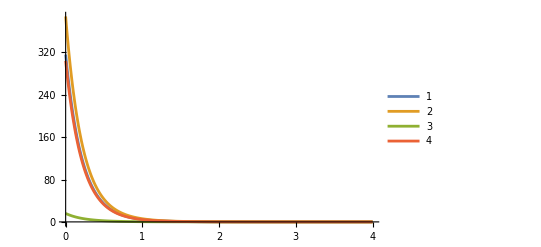

```mathematica
Plot[Evaluate[Subscript[x, l1][t]],{t,0,4},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
Subscript[y, l1][t_]:= Simplify[C1.Subscript[x, l1][t]]
```

```mathematica
Expand[Subscript[y, l1][t]]
```

{-2 ⅇ^(-5 t)-2 ⅇ^(-3 t)}

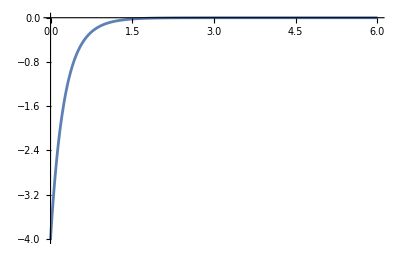

```mathematica
Plot[Subscript[y, l1][t],{t,0,6},PlotRange->All,AspectRatio->Automatic]
```

Caso 2: “attiviamo solo gli ultimi due modi”,trovo un vettore esprimibile come v = α1(T_3)+α1(T_4)

```mathematica
T//MatrixForm
```

(129 | 67 | 29 | 9
155 | 84 | 39 | 14
5 | 4 | 3 | 2
125 | 64 | 27 | 8)

```mathematica
α2 = -3;
```

```mathematica
x2= α2 {{T[[1,2]]},{T[[2,2]]},{T[[3,2]]},{T[[4,2]]}}
```

{{-201},{-252},{-12},{-192}}

```mathematica
z2 = Inverse[T].x2
```

{{0},{-3},{0},{0}}

```mathematica
Subscript[x, l2][t_]:=FullSimplify[∑_(i=1)^n T[[All,i]] ⅇ^(λ[[i]]t)z2[[i,1]]]
```

```mathematica
MatrixForm[Subscript[x, l2][t]]
```

(-201 ⅇ^(-4 t)
-252 ⅇ^(-4 t)
-12 ⅇ^(-4 t)
-192 ⅇ^(-4 t))

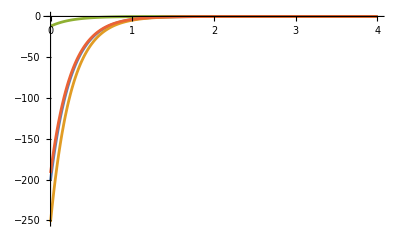

```mathematica
Plot[Evaluate[Subscript[x, l2][t]],{t,0,4},PlotRange->All,AspectRatio->1/GoldenRatio]
```

```mathematica
Subscript[y, l2][t_]:= Simplify[C1.Subscript[x, l2][t]]
```

```mathematica
Expand[Subscript[y, l2][t]]
```

{3 ⅇ^(-4 t)}

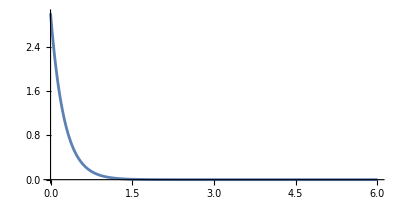

```mathematica
Plot[Subscript[y, l2][t],{t,0,6},PlotRange->All,AspectRatio->Automatic]
```

## 4.La funzione di trasferimento, i suoi poli e zeri

Per motivi di calcolo, è utile rappresentare il nostro sistema in un nuovo dominio. Nel caso TC questo nuovo dominio nella variabile complessa s ci sarà dato dalla trasformata di Laplace. Questo passaggio ci permetterà di calcolare una funzione detta Funzione di Trasferimento(con proprietà molto comode) che a sua volta sarà utile per trovare la risposta forzata del sistema nell’uscita: y_f(t)  prima nel dominio complesso per poi con l’anti trasformata di Laplace riportarla nel dominio del tempo. Caso SISO con LTI-TC la funzione di trasferimento(G(s)) è il prodotto algebrico della L-trasformata dell’ingresso e C(sI_n-A)^-1B + D[quantità scalare legata alle matrici del sistema ed è in funzione di s]. Il nostro sistema è un sistema proprio e dunque D è nulla

```mathematica
pA
```

(2+λc) (3+λc) (4+λc) (5+λc)

Mi calcolo la FdT a partire dalla definizione 
L’inversa della matrice puo anche essere calcolata con adjugate...

```mathematica
G[s_]:=Simplify[C1.Inverse[s IdentityMatrix[4]-A].B][[1]]
```

```mathematica
G[s]
```

{1/(120+154 s+71 s^2+14 s^3+s^4)}

Calcolo ora i poli e gli zeri del sistema:

```mathematica
Solve[Denominator[G[s]]==0]
```

{{s→-5},{s→-4},{s→-3},{s→-2}}

```mathematica
Solve[Numerator[G[s]]==0]
```

{}

Osserviamo due fenomeni “strani”,i poli della Fdt sono un sottoinsieme degli autovalori di A, la funzione di trasferimento non ha zeri. Facciamo la prova del nove per vedere che non abbiamo commesso errori:

```mathematica
Factor[G[s]]
```

{1/((2+s) (3+s) (4+s) (5+s))}

```mathematica
Σ=StateSpaceModel[{A,B,C1}]
```

-12070-103361-12070-1043510-1110-12071-10535110-1-10StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1141FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TransferFunctionModel[Σ]
```

1/(120+154 s+71 s^2+14 s^3+s^4)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s1111201FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TransferFunctionPoles[Σ][[1]][[1]]
```

{-5,-4,-3,-2}

```mathematica
TransferFunctionZeros[Σ]
```

{{{}}}

## 5. La risposta al gradino unitario ed il suo grafico (mettere in evidenza la risposta transitoria e la risposta a regime)

Dopo aver calcolato la Fdt, possiamo procedere allo studio della risposta forzata del sistema al “segnale” del gradino unitario. Il gradino unitario è una funzione definita a tratti che vale 0 per t<0 e 1 per t>=0. Sappiamo che la FDT è definita anche come G(s)=Y(s)/U(s). Possiamo sfruttare questa relazione per trovare l’uscita forzata nel dominio della variabile complessa s sapendo che la L-trasformata del gradino unitario vale 1/s. Ricaviamo la Y(s):

```mathematica
Y[s_]:=Factor[G[s]LaplaceTransform[UnitStep[t],t,s]]
```

```mathematica
Y[s]
```

{1/(s (2+s) (3+s) (4+s) (5+s))}

A questo punto arrivati vogliamo tornare nel dominio del tempo. Sorge un problema ossia dobbiamo utilizzare l’anti trasformata di Laplace, un modo è quello di scomporre l’uscita in fratti semplici e poi sapendo che : 
Scomponiamo  e troviamo le costanti C-iesime con Heaviside elementare :

Osserviamo che la risposta

```mathematica
Subscript[C, 1]=lim_(s->0) s Y[s][[1]]
```

1/120

```mathematica
Subscript[C, 2]=lim_(s->-2) (s+2) Y[s][[1]]
```

-1/12

```mathematica
Subscript[C, 3]=lim_(s->-3) (s+3) Y[s][[1]]
```

1/6

```mathematica
Subscript[C, 4]=lim_(s->-4) (s+4) Y[s][[1]]
```

-1/8

```mathematica
Subscript[C, 5]=lim_(s->-5) (s+5) Y[s][[1]]
```

1/30

```mathematica
Y[s_]:= Subscript[C, 1]/s+Subscript[C, 2]/(s+2)+Subscript[C, 3]/(s+3)+Subscript[C, 4]/(s+4)+Subscript[C, 5]/(s+5)
```

```mathematica
Y[s]
```

1/(120 s)-1/(12 (2+s))+1/(6 (3+s))-1/(8 (4+s))+1/(30 (5+s))

Applichiamo il principio di linearità della L-trasformata con :

```mathematica
Subscript[y, f][t_]:= Subscript[C, 1] 1 + Subscript[C, 2] Exp[-2t]+ Subscript[C, 3] Exp[-3t]+ Subscript[C, 4] Exp[-4t]+ Subscript[C, 5] Exp[-5t]
```

```mathematica
Subscript[y, f][t]
```

1/120+ⅇ^(-5 t)/30-ⅇ^(-4 t)/8+ⅇ^(-3 t)/6-ⅇ^(-2 t)/12

Facciamo la “prova del 9” con la funzione built-in:

```mathematica
Subscript[y, f][t_]:=Expand[InverseLaplaceTransform[G[s]/s,s,t]]
```

```mathematica
Subscript[y, f][t]
```

{1/120+ⅇ^(-5 t)/30-ⅇ^(-4 t)/8+ⅇ^(-3 t)/6-ⅇ^(-2 t)/12}

Anche se non scritto esplicitamente tutti i componenti sono moltiplicati per 1(t) (right-sided). Possiamo dare ora due definizioni a partire dalla risposta forzata, si ha che da quest’ultima si possono ricavare y_ss ossia l’uscita che dipende solo dall’ingresso e y_transitoria le componenti dell’uscita forzata che dipendono anche dai modi naturali.

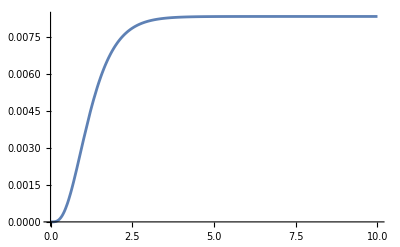

```mathematica
Plot[Subscript[y, f][t],{t,0,10},PlotRange->All]
```

```mathematica
G[0][[1]]
```

1/120

Oltre ad essere la risposta a regime(staedy-state) è anche vista come guadagno statico o guadagno in continua. Osservando la risposta forzata viene intuitivo notare come dopo un certo t la risposta transitoria si esaurisca e permanga solo la risposta a regime che non dipende dal tempo.

```mathematica
Subscript[y, transitoria][t_]:= Subscript[C, 2] Exp[-2t]+ Subscript[C, 3] Exp[-3t]+ Subscript[C, 4] Exp[-4t]+ Subscript[C, 5] Exp[-5t];Subscript[y, transitoria][t]
```

ⅇ^(-5 t)/30-ⅇ^(-4 t)/8+ⅇ^(-3 t)/6-ⅇ^(-2 t)/12

```mathematica
Subscript[y, ss][t_]:=  Subscript[C, 1] 1 ;Subscript[y, ss][t]
```

1/120

```mathematica
Plot[{Subscript[y, transitoria][t],Subscript[y, ss][t],Subscript[y, f][t]},{t,0,4},PlotRange->All,PlotLabels->{"Transitoria","Steady-State","Forzata"}]
```

-Graphics-

## 6.La risposta al segnale periodico elementare u(t) = A sin(ωt + ψ)1(t) (lo studente scelga una terna appropriata di valori A, ω, ψ e discuta le caratteristiche di tale risposta forzata in maniera simile al punto precedente);

Occupiamoci di una nuova risposta forzata ad un segnale periodico right-sided u(t) = Asin(ωt +ψ) , con A = ampiezza,ω=pulsazione  e ψ=sfasamento iniziale, di cui conosciamo la sua trasformata di Laplace     
con U ampiezza complessa : U = Ae^{jθ}. Parte di teoria

```mathematica
Amp =1;ω=1;ψ=0;
```

```mathematica
Subscript[U, sin][s_]:=LaplaceTransform[Amp *Sin[ω t+ψ]UnitStep[t],t,s];
```

```mathematica
Subscript[U, sin][s]
```

1/(1+s^2)

```mathematica
Subscript[Y, sin][s_]:= G[s]*Subscript[U, sin][s]
```

```mathematica
Apart[Subscript[Y, sin][s]]
```

{1/(30 (2+s))-1/(20 (3+s))+1/(34 (4+s))-1/(156 (5+s))+(5-14 s)/(2210 (1+s^2))}

```mathematica
Factor[Subscript[Y, sin][s]]
```

{1/((2+s) (3+s) (4+s) (5+s) (1+s^2))}

Notiamo come  sia una funzione “real-razionale”  e al suo denominatore appaiono i primi 4 fattori legati ai modi naturali del sistema e l’ultimo legato all’ingresso. Proprio di quest’ultimo sappiamo che possiamo scomporlo come , utilizziamo Heaviside per trovare le costanti della  .

```mathematica
Subscript[D, 1]= lim_(s->-I) (s+I) Subscript[Y, sin][s]; Subscript[D̄, 1]= lim_(s->I) (s-I) Subscript[Y, sin][s][[1]]; Subscript[D, 2]= lim_(s->-2) (s+2) Subscript[Y, sin][s][[1]];Subscript[D, 3]= lim_(s->-3) (s+3) Subscript[Y, sin][s][[1]];Subscript[D, 4]= lim_(s->-4) (s+4) Subscript[Y, sin][s][[1]];Subscript[D, 5]= lim_(s->-5) (s+5)Subscript[Y, sin][s][[1]];
```

```mathematica
Subscript[y, fSin][t_]:= Subscript[D, 1]/(s+I)+Subscript[D̄, 1]/(s-I)+Subscript[D, 2]/(s+2)+Subscript[D, 3]/(s+3)+Subscript[D, 4]/(s+4)+Subscript[D, 5]/(s+5)
```

```mathematica
Subscript[y, fSin][t]
```

{-(7/2210+ⅈ/884)/(-ⅈ+s)-(7/2210-ⅈ/884)/(ⅈ+s)+1/(30 (2+s))-1/(20 (3+s))+1/(34 (4+s))-1/(156 (5+s))}

Delle ultime quattro componenti (legate ai modi naturali)conosco già l’antitrasformata di Laplace, dei primi due(legati all’ingresso) invece so che sono complessi e coniugati dunque vale   e posso applicare :

```mathematica
Subscript[y, ssSin][t_]:=  ComplexExpand[2Re[Subscript[D̄, 1] Exp[I t]]];Subscript[y, ssSin][t]
```

-(7 Cos[t])/1105+Sin[t]/442

```mathematica
Subscript[y, tSin][t_] :=Subscript[D, 2] Exp[-2t]+ Subscript[D, 3] Exp[-3t]+ Subscript[D, 4] Exp[-4t]+ Subscript[D, 5] Exp[-5t];Subscript[y, tSin][t]
```

-1/156 ⅇ^(-5 t)+ⅇ^(-4 t)/34-ⅇ^(-3 t)/20+ⅇ^(-2 t)/30

```mathematica
Subscript[y, fSin][t_]:= (Subscript[y, tSin][t]+ Subscript[y, ssSin][t]);Subscript[y, fSin][t]
```

-1/156 ⅇ^(-5 t)+ⅇ^(-4 t)/34-ⅇ^(-3 t)/20+ⅇ^(-2 t)/30-(7 Cos[t])/1105+Sin[t]/442

```mathematica
Plot[{-1/156 ⅇ^(-5 t)+ⅇ^(-4 t)/34-ⅇ^(-3 t)/20+ⅇ^(-2 t)/30,-(7 Cos[t])/1105+Sin[t]/442,-1/156 ⅇ^(-5 t)+ⅇ^(-4 t)/34-ⅇ^(-3 t)/20+ⅇ^(-2 t)/30-(7 Cos[t])/1105+Sin[t]/442},{t,0,3},PlotRange->All,PlotLabels->{"Transitoria","Steady-State","Forzata"}]
```

-Graphics-

Controlliamone la correttezza utilizzando la funzione built-in:

```mathematica
Subscript[y, fSin][t_]:= Expand[InverseLaplaceTransform[Subscript[Y, sin][s],s,t]]
```

```mathematica
Subscript[y, fSin][t]
```

{-1/156 ⅇ^(-5 t)+ⅇ^(-4 t)/34-ⅇ^(-3 t)/20+ⅇ^(-2 t)/30-(7 Cos[t])/1105+Sin[t]/442}

Uso il teorema della risposta armonica per verificare

```mathematica
Subscript[y, ssSin][t_]:=Abs[G[I ω]] Amp Sin[ω t + ψ+ Arg[G[I ω]]]
```

```mathematica
Subscript[y, ssSin][t]
```

{Sin[t-ArcTan[14/5]]/(10 √221)}

Adesso posso trovare  y_tsin = y_fsin - y_sssin

```mathematica
Subscript[y, tSin][t_]:= (Subscript[y, fSin][t]-Subscript[y, ssSin][t])
```

```mathematica
Subscript[y, tSin][t]
```

{-1/156 ⅇ^(-5 t)+ⅇ^(-4 t)/34-ⅇ^(-3 t)/20+ⅇ^(-2 t)/30-(7 Cos[t])/1105+Sin[t]/442-Sin[t-ArcTan[14/5]]/(10 √221)}

```mathematica
Plot[{-1/156 ⅇ^(-5 t)+ⅇ^(-4 t)/34-ⅇ^(-3 t)/20+ⅇ^(-2 t)/30-(7 Cos[t])/1105+Sin[t]/442-Sin[t-ArcTan[14/5]]/(10 √221),Sin[t-ArcTan[14/5]]/(10 √221),
-1/156 ⅇ^(-5 t)+ⅇ^(-4 t)/34-ⅇ^(-3 t)/20+ⅇ^(-2 t)/30-(7 Cos[t])/1105+Sin[t]/442},{t,0,3},PlotRange->All,PlotLabels->{"Transitoria","Steady-State","Forzata"}]
```

-Graphics-

Invece di apart avremmo potuto usare di nuovo Heaviside per “spacchettare ” la nostra uscita complessa e poi trasformarla.

## 7. Un suo modello ARMA equivalente, individuando le condizioni iniziali sull’uscita compatibili con lo stato iniziale x_i[0 -2 -2 3]^T. Una volta individuata tale rappresentazione e le condizioni iniziali sull’uscita valutare la risposta alla rampa unitaria (no grafico) mettendo in evidenza la risposta transitoria (risposta libera inclusa) e la componente legata algebricamente all’ingresso

Il passaggio da modello I/S/U a I/U si fa sfruttando la FDT che rimane invariata e il teorema della derivata caso tempo continuo. Per definizione    e dunque G(s) è una frazione scomponibile in numeratore e denominatore n_G e d_G →

```mathematica
Subscript[Eq, iu][s] :=Expand[Denominator[G[s][[1]]] Subscript[Y, iu][s]==Expand[Numerator[G[s][[1]]] Subscript[U, iu][s]]]
```

```mathematica
Subscript[Eq, iu][s]
```

120 Y_iu[s]+154 s Y_iu[s]+71 s^2 Y_iu[s]+14 s^3 Y_iu[s]+s^4 Y_iu[s]==U_iu[s]

Applicchiamo ora il teorema delle derivate insieme all’anti-trasformata di Laplace

```mathematica
InverseLaplaceTransform[Subscript[Eq, iu][s],s,t]
```

120 InverseLaplaceTransform[Y_iu[s],s,t]+154 InverseLaplaceTransform[s Y_iu[s],s,t]+71 InverseLaplaceTransform[s^2 Y_iu[s],s,t]+14 InverseLaplaceTransform[s^3 Y_iu[s],s,t]+InverseLaplaceTransform[s^4 Y_iu[s],s,t]==InverseLaplaceTransform[U_iu[s],s,t]

```mathematica
eq=InverseLaplaceTransform[Subscript[Eq, iu][s],s,t]/.{Subscript[Y, iu][s]->LaplaceTransform[Subscript[y, iu][t],t,s],Subscript[U, iu][s]->LaplaceTransform[Subscript[u, iu][t],t,s]}/.{Subscript[y, iu][0]->0,Subscript[y, iu]'[0]->0,Subscript[y, iu]''[0]->0,Subscript[y, iu]'''[0]->0,Subscript[y, iu]''''[0]->0,Subscript[u, iu][0]->0}
```

120 y_iu[t]+154 y_iu'[t]+71 y_iu''[t]+14 y_iu^(3)[t]+y_iu^(4)[t]==u_iu[t]

Come vediamo abbiamo posto le condizioni iniziali y[0] nulle essendo la risposta forzata. A questo punto arrivati abbiamo ottenuto un eq.diff che rappresenta il modello I/U del sistema nel tempo.Definiamo il nostro nuovo stato iniziale tale che il nostro sistema sia compatibile con esso

```mathematica
Subscript[x, i] = {{0},{-2},{-2},{3}}
```

{{0},{-2},{-2},{3}}

```mathematica
Subscript[x, i]//MatrixForm
```

(0
-2
-2
3)

so che la risposta libera y_iu(t) = Cx(t) + 0 igresso nullo. Se itero le derivate ottengo espressioni del tipo:
 𝑦_0 = 𝐶 𝑥_0; 𝑦_0’= 𝐶 𝑥_0' = 𝐶 𝐴 𝑥_0, continuando a iterare arrivo a :y_0^{𝑛−1}= CA^{n-1}x_0

```mathematica
Subscript[y, 0][0]=(C1.Subscript[x, i]) [[1,1]]
```

-1

```mathematica
Subscript[y, 0]'[0]=(C1.A.Subscript[x, i])[[1,1]]
```

-2

```mathematica
Subscript[y, 0]''[0]=(C1.A.A.Subscript[x, i])[[1,1]]
```

3

```mathematica
Subscript[y, 0]'''[0]=(C1.A.A.A.Subscript[x, i])[[1,1]]
```

3

```mathematica
Subscript[y, 0]''''[0]=(C1.A.A.A.A.Subscript[x, i])[[1,1]]
```

173

Dopo aver trovato le soluzioni iniziali lato uscita posso ritornare al dominio s:

```mathematica
eqD= LaplaceTransform[120 y[t]+154 y'[t]+71 y''[t]+14 Derivative[3][y][t]+Derivative[4][y][t]==u[t] ,t,s]/.{LaplaceTransform[y[t],t,s]->Subscript[Y, IU][s],LaplaceTransform[u[t],t,s]->Subscript[U, IU][s]}
```

-s^3 y[0]+120 Y_IU[s]+s^4 Y_IU[s]+154 (-y[0]+s Y_IU[s])+71 (-s y[0]+s^2 Y_IU[s]-y'[0])-s^2 y'[0]+14 (-s^2 y[0]+s^3 Y_IU[s]-s y'[0]-y''[0])-s y''[0]-y^(3)[0]==U_IU[s]

```mathematica
Solve[eqD,Subscript[Y, IU][s]][[1,1]][[2]]
```

(154 y[0]+71 s y[0]+14 s^2 y[0]+s^3 y[0]+U_IU[s]+71 y'[0]+14 s y'[0]+s^2 y'[0]+14 y''[0]+s y''[0]+y^(3)[0])/(120+154 s+71 s^2+14 s^3+s^4)

Separiamo le componenti della risposta libera e forzata, raccogliendo l’ingresso U(s)

```mathematica
Collect[Solve[eqD,Subscript[Y, IU][s]][[1,1]][[2]],Subscript[U, IU][s]]
```

U_IU[s]/(120+154 s+71 s^2+14 s^3+s^4)+(154 y[0]+71 s y[0]+14 s^2 y[0]+s^3 y[0]+71 y'[0]+14 s y'[0]+s^2 y'[0]+14 y''[0]+s y''[0]+y^(3)[0])/(120+154 s+71 s^2+14 s^3+s^4)

Pertanto possiamo notare come il primo membro della somma(dipendente da U_IU e senza condizioni iniziali ) è la risposta forzata mentre il secondo membro è la risposta libera non dipendendo dall’ingresso:

```mathematica
Subscript[Y, FIU][s_]:=Collect[Solve[eqD,Subscript[Y, IU][s]][[1,1]][[2]],Subscript[U, IU][s]][[1]];Subscript[Y, FIU][s]
```

U_IU[s]/(120+154 s+71 s^2+14 s^3+s^4)

```mathematica
Subscript[Y, LIU][s_]:=Collect[Solve[eqD,Subscript[Y, IU][s]][[1,1]][[2]],Subscript[U, IU][s]][[2]];Subscript[Y, LIU][s]
```

(154 y[0]+71 s y[0]+14 s^2 y[0]+s^3 y[0]+71 y'[0]+14 s y'[0]+s^2 y'[0]+14 y''[0]+s y''[0]+y^(3)[0])/(120+154 s+71 s^2+14 s^3+s^4)

A quest’ultima andranno sostituiti i valori delle condizioni iniziali nell’uscita precedentemente calcolati partendo dallo stato iniziale

```mathematica
Subscript[Y, LIU][s]/.{y[0]->Subscript[y, 0][0],y'[0]->Subscript[y, 0]'[0],y''[0]->Subscript[y, 0]''[0],y'''[0]->Subscript[y, 0]'''[0],y''''[0]->Subscript[y, 0]''''[0]}
```

(-251-96 s-16 s^2-s^3)/(120+154 s+71 s^2+14 s^3+s^4)

Che portata nel dominio del tempo sarà:

```mathematica
Subscript[y, LIU][t_]:= InverseLaplaceTransform[(-251-96 s-16 s^2-s^3)/(120+154 s+71 s^2+14 s^3+s^4),s,t];Subscript[y, LIU][t]
```

1/6 ⅇ^(-5 t) (46-177 ⅇ^t+240 ⅇ^(2 t)-115 ⅇ^(3 t))

Si noti che la risposta libera calcolata a partire dalla rappresentazione IU rimane  invariata se calcolata a partire dalla rappresentazione I/S/U

```mathematica
InverseLaplaceTransform[C1.Inverse[s IdentityMatrix[4]-A].Subscript[x, i],s,t][[1,1]]
```

1/6 ⅇ^(-5 t) (46-177 ⅇ^t+240 ⅇ^(2 t)-115 ⅇ^(3 t))

Per il calcolo della risposta forzata alla rampa procedo ora moltiplicando la L-TRASFORMATA della rampa alla Y_FIU(s) trovata a partire dal modello I/U

```mathematica
Subscript[Y, FIU][s_]:= Apart[(-251-96 s-16 s^2-s^3)/(120+154 s+71 s^2+14 s^3+s^4)LaplaceTransform[t UnitStep[t],t,s]];Subscript[Y, FIU][s]
```

-251/(120 s^2)+13567/(7200 s)-115/(24 (2+s))+40/(9 (3+s))-59/(32 (4+s))+23/(75 (5+s))

Per non tediare troppo con i calcoli in questo passaggio sfruttiamo la funzione Apart che ci permette di scomporre la risposta in fratti semplici. 
A questo punto arrivati e grazie ad apart conosciamo i coefficienti e sappiamo chi sono le anti trasformate :

Implicitamente moltiplicate per 1(t):

```mathematica
Subscript[y, RFIU][t_]:= -251/120 t 1 +13567/7200 1-115/24 Exp[-2t]1+40/9 Exp[-3t]1-59/32 Exp[-4t]1+23/75 Exp[-5t]1;Subscript[y, RFIU][t]
```

```mathematica
13567/7200-(251 t)/120+(23 ⅇ^(-5 t))/75-(59 ⅇ^(-4 t))/32+(40 ⅇ^(-3 t))/9-(115 ⅇ^(-2 t))/24
```

Salta subito all’occhio come la componente legata ai modi naturali(ossia risposta transitoria) per t che va a  infinito converga, lasciando solo la componente a regime che però a causa dell’ingresso esplosivo(la rampa) non converge

## 8. Determinare lo stato iniziale x0 tale che la risposta al gradino coincida con il suo valore di regime(assenza di componente transitoria).

Per riuscire a determinare lo stato iniziale x_(0i)tale che soddisfi le caratteristiche richieste sull’uscita possiamo procedere in due modi. Il primo modo e tramite la funzione di trasferimento trovare l’uscita e calcolare i fratti semplici, oppure il secondo modo sfuttando il teorema del valore finale. La nostra soluzione sfrutterà quest’ultimo metodo che ci assicura nel caso in cui il sistema sia BIBO stabile e che la funzione su cui vogliamo appicare il teroema siadontinua e di classe L. Come visto nei casi precedenti il nostro sistema è BIBO stabile ed essendo LTI la nostra risposta forzata sarà composta da risposta ss + transitoria. Il teorema ci assicura l’esistenza di unvalore   allora  : . Nel nostro caso specifico abbiamo che  dove

dove U è l’ampiezza del gradino. Applichiamo il teorema del valore finale , G(0) è anche detto guadagno statico o in continua.

Rappresento la risposta forzata, considero il gradino unitario U=1:

```mathematica
U=1;
```

```mathematica
Subscript[Y, FU][s_]:= Factor[G[s] U/s];Subscript[Y, FU][s]
```

{1/(s (2+s) (3+s) (4+s) (5+s))}

```mathematica
Subscript[Y, ssU][s_]:= G[0] U/s;
```

```mathematica
Subscript[Y, trU][s_]:=Factor[Subscript[Y, FU][s] - Subscript[Y, ssU][s]];Subscript[Y, trU][s]
```

{-((7+s) (22+7 s+s^2))/(120 (2+s) (3+s) (4+s) (5+s))}

Poichè il sistema è  LTI

Scrivo lo stato iniziale incognito :

```mathematica
Subscript[x, i0]={{Subscript[x, 1]},{Subscript[x, 2]},{Subscript[x, 3]},{Subscript[x, 4]}}
```

{{x_1},{x_2},{x_3},{x_4}}

```mathematica
Subscript[Y, L][s_]:= FullSimplify[C1.Inverse[s IdentityMatrix[4]-A].Subscript[x, i0]][[1,1]];Subscript[Y, L][s]
```

-(-((7+s) (22+s (7+s)) x_1)+(14+s) x_2+(69+s (56+s (13+s))) x_3+(139+s (70+s (14+s))) x_4)/((2+s) (3+s) (4+s) (5+s))

Per vedere quali valori della mia x_i0 annulla la Y_0 mi basta vadere quali valori annullano il suo numeratore.

```mathematica
coefList = CoefficientList[Numerator[Simplify[Expand[ Subscript[Y, L][s] + Subscript[Y, trU][s]]]],s ][[1]]
```

{-154+18480 x_1-1680 x_2-8280 x_3-16680 x_4,-71+8520 x_1-120 x_2-6720 x_3-8400 x_4,-14+1680 x_1-1560 x_3-1680 x_4,-1+120 x_1-120 x_3-120 x_4}

Determino ora le incognite x_i che annullano il set dei coefficienti del polinomio al numeratore di libera+forzata

```mathematica
Solve[coefList=={0,0,0,0},{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4]}]
```

{{x_1→1/120,x_2→0,x_3→0,x_4→0}}

Effettuo la verifica, prima con la funzione built-in e poi “a mano”.

```mathematica
Subscript[Y, ssU][s]
```

{1/(120 s)}

```mathematica
OutputResponse[{Σ,{1/120,0,0,0}},1,t]
```

{1/120}

Faccio ora anche la verifica “manuale”

```mathematica
Subscript[x, i0]={{1/120},{0},{0},{0}};
```

```mathematica
Subscript[Y, L0][s_]:= FullSimplify[C1.Inverse[s IdentityMatrix[4]-A].Subscript[x, i0]][[1,1]];Subscript[Y, L0][s]
```

((7+s) (22+s (7+s)))/(120 (2+s) (3+s) (4+s) (5+s))

```mathematica
Simplify[Subscript[Y, L0][s]+Subscript[Y, trU][s]]
```

{0}

```mathematica
Subscript[y, L][t_]:=InverseLaplaceTransform[Subscript[Y, L][s],s,t];Subscript[y, ssU][t_]:=InverseLaplaceTransform[Subscript[Y, ssU][s],s,t];Subscript[y, fUz][t_]:=InverseLaplaceTransform[Subscript[Y, FU][s],s,t];
```

```mathematica
Plot[{Subscript[y, L][t],Subscript[y, ssU][t],Subscript[y, fUz][t]},{t,0,4},PlotRange->All,PlotLabels->{Libera,Steady-State,Forzata}]
```

-Graphics-

## 9. Valutare la risposta al segnale u(t) = 1(−t)

Il calcolo della risposta all’ingresso 1(-t) presuppone la BIBO stabilita’ (Asintotica Stabilita’). Si seguono due step: valutazione della risposta per t<0 (finito), valutazione della risposta per t>0 (finito).
1.Valuto la risposta a regime(valutazione della risposta per t<0 finito):

```mathematica
G[s_]:=Simplify[(C1.Inverse[s IdentityMatrix[4]-A].B)[[1]][[1]]];G[s]
```

1/(120+154 s+71 s^2+14 s^3+s^4)

```mathematica
Subscript[y, negativa] = G[0]
```

1/120

2. Valutazione della risposta per t>0. E’ la risposta del sistema in assenza di ingresso ma A PARTIRE DALLE CONDIZIONI INIZIALI LEGATE ALLA COMMUTAZIONE DA 1 a 0. Per continuita’ valgono queste relazioni y(0-) = y(0+), y’(0-) = y’(0+).... Mi ricavo lo stato iniziale risolvendo il sistema O x0 = cond.iniziali. Si sfrutta la matrice di osservabilità

```mathematica
Obs = {C1[[1]],(C1.A)[[1]],(C1.A.A)[[1]],(C1.A.A.A)[[1]] }
```

{{1,0,-1,-1},{0,0,1,0},{0,-1,1,1},{0,0,0,1}}

```mathematica
Obs//MatrixForm
```

```mathematica
({{1, 0, -1, -1}, {0, 0, 1, 0}, {0, -1, 1, 1}, {0, 0, 0, 1}})
```

Controllo sia invertibile:

```mathematica
Det[Obs]
```

1

Mi ricavo le condizioni iniziali a partire dal sistema x_0 = 0 Obs^-1

```mathematica
Subscript[x, 0]=Inverse[Obs].{{G[0]},{0},{0},{0}}
```

{{1/120},{0},{0},{0}}

```mathematica
Ylib =Simplify[(C1.Inverse[s IdentityMatrix[4]-A].Subscript[x, 0])[[1]][[1]]]
```

(154+71 s+14 s^2+s^3)/(120 (120+154 s+71 s^2+14 s^3+s^4))

```mathematica
Apart[Ylib]
```

1/(12 (2+s))-1/(6 (3+s))+1/(8 (4+s))-1/(30 (5+s))

```mathematica
ylibt = 1/12 Exp[-2t]-1/6 Exp[-3t]+1/8 Exp[-4t]-1/30 Exp[-5t]
```

-1/30 ⅇ^(-5 t)+ⅇ^(-4 t)/8-ⅇ^(-3 t)/6+ⅇ^(-2 t)/12

```mathematica
Subscript[y, nUnitStep][t_]:=Piecewise[{{Subscript[y, negativa], t<0}, {ylibt, t>=0}}]
```

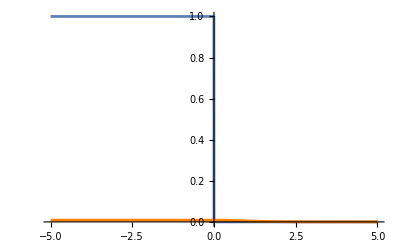

```mathematica
Plot[{UnitStep[-t],Subscript[y, nUnitStep][t]},{t,-5,5},PlotRange->All,Exclusions->None,PlotStyle->{,Orange}]
```

Vediamo la nostra risposta da piu vicino:

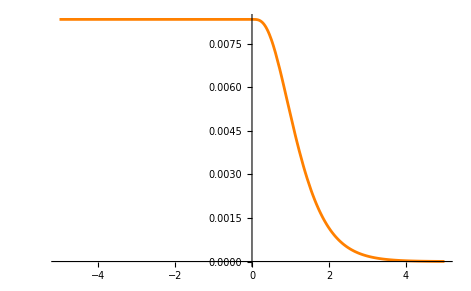

```mathematica
Plot[{Subscript[y, nUnitStep][t]},{t,-5,5},PlotRange->All,Exclusions->None,PlotStyle->Orange]
```